# Prédire le type des Pokémon inconnus : un pari gagnant ? -Graphics-

## Introduction :

Dans le cadre de la SAÉ S4.03 – “Traitement et visualisation d’un jeu de données” – chaque étudiant est invité à explorer librement un ensemble de données à travers une approche descriptive ou mathématique, avec une forte attention portée à la qualité des représentations visuelles.

J’ai choisi de m’orienter vers une analyse statistique descriptive appliquée à un univers riche et structuré : l’univers des Pokémon. Ces créatures fictives, connues mondialement, sont classées selon plusieurs types (eau, feu, plante, etc.) et caractérisées par des statistiques de combat (attaque, défense, vitesse, etc.).

Ma problématique principale est la suivante :

Peut-on prédire le ou les types d’un Pokémon à partir de ses statistiques ?
 
Ou au contraire, ces types sont-ils définis de manière arbitraire par les créateurs, sans lien réel avec les données chiffrées ?

Ce projet propose donc une exploration statistique autour de cette idée : chercher à identifier des regroupements naturels dans l’espace des statistiques, via des techniques de clustering non supervisé telles que KMeans ou CAH (Classification Ascendante Hiérarchique), et analyser si ces regroupements correspondent ou non aux types connus.

L’objectif final est double :

Comprendre s’il existe une cohérence statistique entre les types.

Explorer les possibilités de prédiction ou d’approximation automatique du type d’un Pokémon via ses caractéristiques numériques.

Ce travail mobilise à la fois des compétences en préparation de données, normalisation, choix de métriques, et bien sûr, visualisation pour interpréter les regroupements obtenus.

## Importation et préparation des données

```mathematica
(* 📥 Importation du fichier Pokémon *)
df = Import[FileNameJoin[{NotebookDirectory[], "pokemon", "pokemon.csv"}], "Dataset"];


(* 📊 Colonnes de stats *)
statsCols = {"hp", "attack", "defense", "sp_attack", "sp_defense", "speed"};

(* 🧹 Nettoyage : on garde seulement les lignes avec toutes les stats numériques *)
dfClean = Select[df, AllTrue[statsCols, Function[col, NumericQ[Lookup[#, col, Missing[]]]]] &];

Print["✅ Données importées et nettoyées. ", Length[dfClean], " Pokémon valides."];
```

## Visualisation de cluster simple

Ce bloc de code a pour but de réaliser un test visuel simple du clustering KMeans sur trois statistiques : “hp”, “attack” et “speed”, avec un nombre de clusters fixé arbitrairement à k = 4.

L’objectif ici n’est pas de déterminer les meilleurs paramètres, mais simplement de :

Vérifier que la procédure de standardisation et de clustering fonctionne correctement ;

Observer à quoi ressemble un regroupement visuel dans un espace à 2 ou 3 dimensions.

Il s’agit donc d’une première expérimentation exploratoire, sans prétention d’optimisation, qui servira plus tard à nourrir l’outil de visualisation dynamique du projet.

```mathematica
(* 📌 Paramètres *)
selectedStats = {"hp", "attack", "speed"};
k = 4;

(* Extraction des données *)
X = Normal[dfClean[[All, selectedStats]]];
XMatrix = Values /@ X;
XStandardized = Standardize /@ Transpose[XMatrix] // Transpose;

(* Clustering KMeans *)
clusters = FindClusters[XStandardized, k, Method -> "KMeans"];

Print["✅ Clustering effectué avec succès sur ", selectedStats, " | k = ", k, "."];

(* ✅ Conversion en nombres réels *)
pointsByCluster = Map[N, clusters, {2}];

(* 🖼️ Affichage dynamique selon le nombre de stats *)
Which[
  Length[selectedStats] == 2,
  ListPlot[
    pointsByCluster,
    PlotStyle -> PointSize[Medium],
    AxesLabel -> selectedStats,
    PlotLabel -> Style["Clustering 2D", Bold, 14],
    PlotLegends -> Placed[Automatic, Right]
  ],
  
  Length[selectedStats] == 3,
  Graphics3D[
    Table[
      {ColorData[97][i], PointSize[Medium], Point[pointsByCluster[[i]]]},
      {i, Length[pointsByCluster]}
    ],
    Axes -> True,
    AxesLabel -> selectedStats,
    PlotLabel -> Style["Clustering 3D", Bold, 14]
  ],
  
  True,
  Print["❌ Il faut 2 ou 3 dimensions pour visualiser le clustering."]
]
```

Ce graphique montre une première visualisation 3D du clustering KMeans appliqué aux statistiques “hp”, “attack” et “speed”. On observe la formation de groupes distincts dans l’espace des caractéristiques, ce qui suggère l’existence de structures naturelles parmi les Pokémon selon ces critères.

## Outil de visualisation des clusterings

## Visualistaion interactive des clusters

L’outil de visualisation développé dans ce projet constitue une interface interactive permettant d’explorer les regroupements statistiques formés par différents algorithmes de clustering appliqués aux Pokémon. Il repose sur la sélection libre de deux ou trois caractéristiques numériques parmi les statistiques de combat classiques telles que les points de vie (hp), l’attaque, la défense ou la vitesse. Grâce à un menu déroulant, l’utilisateur peut choisir les variables qu’il souhaite analyser, le nombre de groupes à générer (k), ainsi que la méthode de clustering : KMeans ou CAH (Classification Ascendante Hiérarchique).

Cette interface offre également des options de filtrage permettant de restreindre l’analyse à un type spécifique de Pokémon ou de ne considérer que les Pokémon légendaires ou non légendaires. Une fois les paramètres définis, les données sont automatiquement filtrées, standardisées, et utilisées pour générer un clustering. Si deux variables sont sélectionnées, le résultat est affiché dans un plan 2D ; si trois sont choisies, un graphique 3D est généré, chaque cluster étant représenté par une couleur différente pour faciliter la lecture.

L’intérêt de cet outil est de permettre une exploration libre et intuitive des structures présentes dans les données, et d’observer si certains regroupements statistiques semblent correspondre aux types définis par les concepteurs du jeu.
 En laissant à l’utilisateur la liberté de tester différentes combinaisons.

```mathematica
donnees = Import[FileNameJoin[{NotebookDirectory[], "pokemon", "pokemon.csv"}], "Dataset"];

statsColonnes = {"hp", "attack", "defense", "sp_attack", "sp_defense", "speed"};
typeColonnes = {"type1", "type2"};
allTypes = DeleteDuplicates[Flatten[Values /@ donnees[[All, typeColonnes]]]];
allTypesClean = DeleteCases[allTypes, _Missing];

DynamicModule[
  {
    stat1 = "None", stat2 = "None", stat3 = "None",
    selectedK = 3, typeFilter = "Tous", legendaryFilter = "Tous",
    methodChoice = "KMeans"
  },
  
  Column[{
  
    Style["🔍 Interface interactive de clustering dynamique", Bold, 16],
    
    Row[{"📊 Statistique 1 : ", PopupMenu[Dynamic[stat1], Prepend[statsColonnes, "None"]]}],
    Row[{"Statistique 2 : ", PopupMenu[Dynamic[stat2], Prepend[statsColonnes, "None"]]}],
    Row[{"Statistique 3 : ", PopupMenu[Dynamic[stat3], Prepend[statsColonnes, "None"]]}],
    
    Row[{"🔹 k (nombre de clusters) : ", Slider[Dynamic[selectedK], {2, 20, 1}], Dynamic[selectedK]}],
    
    Row[{"🔧 Méthode : ", PopupMenu[Dynamic[methodChoice], {"KMeans", "CAH"}]}],
    
    Row[{
      "🧬 Type : ",
      PopupMenu[Dynamic[typeFilter], Prepend[{
        "grass", "water", "fire", "electric", "psychic", "ghost", "normal",
        "fighting", "flying", "poison", "ground", "rock", "bug", "ice",
        "dragon", "dark", "steel", "fairy"
      }, "Tous"]]
    }],
		    
    Row[{"✨ Légendaire : ", PopupMenu[Dynamic[legendaryFilter], {"Tous", "1", "0"}]}],
    
    Dynamic[
      Module[{selectedStats, filtered, X, XMatrix, XStandardized, clusters, pointsByCluster},
      
        selectedStats = DeleteCases[{stat1, stat2, stat3}, "None"];
        
        If[Length[selectedStats] < 2 || Length[selectedStats] > 3,
          Return[Style["❌ Choisis 2 ou 3 statistiques différentes.", Red]]
        ];
        
        filtered = Quiet@Check[Normal[donnees], {}];
        
        If[typeFilter =!= "Tous",
          filtered = Select[filtered, #["type1"] === typeFilter &]
        ];
        
        If[legendaryFilter =!= "Tous",
          filtered = Select[filtered, ToString[#["is_legendary"]] === legendaryFilter &]
        ];
        
        If[Length[filtered] < selectedK,
          Return[Style["⚠️ Pas assez de données pour k = " <> ToString[selectedK], Red]]
        ];
        
        X = filtered[[All, selectedStats]];
        XMatrix = Values /@ X;
        XStandardized = N[Transpose[Standardize /@ Transpose[XMatrix]]];
        
			clusters = Which[
			  methodChoice === "KMeans",
			    FindClusters[XStandardized, selectedK, Method -> "KMeans"],
			
			  methodChoice === "CAH",
			    FindClusters[XStandardized, selectedK, Method -> "Agglomerate"],
			
			  True,
			    {}
			];

        
        pointsByCluster = Map[N, clusters, {2}];
        
        Which[
          Length[selectedStats] == 2,
          ListPlot[
            Table[pointsByCluster[[i]], {i, Length[pointsByCluster]}],
            PlotStyle -> Table[{ColorData[97][i], PointSize[Medium]}, {i, Length[pointsByCluster]}],
            PlotMarkers -> Automatic,
            AxesLabel -> selectedStats,
            PlotLabel -> Style["Clustering 2D (" <> methodChoice <> ")", Bold, 14],
            PlotLegends -> Placed[Automatic, Right]
          ],
          
          Length[selectedStats] == 3,
          Graphics3D[
            Table[
              {ColorData[97][i], PointSize[Medium], Point[pointsByCluster[[i]]]},
              {i, Length[pointsByCluster]}
            ],
            Axes -> True,
            AxesLabel -> selectedStats,
            PlotLabel -> Style["Clustering 3D (" <> methodChoice <> ")", Bold, 14]
          ],
          
          True,
          Style["❌ Choisis 2 ou 3 statistiques seulement.", Red]
        ]
      ]
    ]
  }]
]
```

En CAH, on observe souvent un gros bloc de points regroupés dans un seul cluster, contrairement à KMeans. Cela vient du fait que la CAH fonctionne par fusions successives : elle commence par rassembler les points les plus proches, ce qui forme rapidement un cluster central très dense. Si une grande partie des données est homogène, elle sera vite fusionnée, laissant peu de points à répartir dans les autres groupes. KMeans, lui, cherche à répartir les points de manière plus équilibrée autour de centres, ce qui évite ce déséquilibre. Ainsi, CAH met en évidence la structure naturelle des données, mais peut créer des clusters très déséquilibrés visuellement.

## Calcul des meilleurs clusterings

Ce bloc de code a pour objectif d’identifier les combinaisons de statistiques qui produisent les meilleurs regroupements en termes de cohérence interne, à l’aide d’algorithmes de clustering non supervisés. Pour cela, on teste systématiquement toutes les combinaisons possibles de deux ou trois statistiques parmi les six proposées (hp, attack, defense, sp_attack, sp_defense, speed). Pour chaque combinaison, on applique le clustering KMeans (ou CAH si choisi), en faisant varier la valeur de k entre 2 et 10. On mesure ensuite la variance intra-cluster, c’est-à-dire la dispersion des points autour de leur centre de gravité, et on enregistre cette mesure pour chaque essai.

Après avoir effectué tous les calculs, les résultats sont triés par variance croissante afin de faire ressortir les combinaisons les plus compactes, donc potentiellement les plus significatives en termes de regroupement.

```mathematica
(* Choix des stats de base *)
statsList = {"hp", "attack", "defense", "sp_attack", "sp_defense", "speed"};

(* Données filtrées *)
Xdata = Normal[donnees];
XdataClean = Select[Xdata, FreeQ[#, _Missing] &];

(* Combinaisons de stats 2 et 3 à tester *)
combinaisons = Join[
  Subsets[statsList, {2}],
  Subsets[statsList, {3}]
];

(* Méthode à tester : "KMeans" ou "CAH" *)
method = "KMeans"; (* ou "CAH" *)

(* Calcul de la variance intra-classe pour chaque combinaison et chaque k *)
results = Reap[
  Do[
    stats = combo;
    X = XdataClean[[All, stats]];
    Xmatrix = N[Transpose[Standardize /@ Transpose[Values /@ X]]];
    
Do[
  clusters = Which[
    method === "KMeans",
      FindClusters[Xmatrix, k, Method -> "KMeans"],
    method === "CAH",
      Module[{linkage, labels},
        linkage = Agglomerate[Xmatrix, "Ward"];
        labels = CutTree[linkage, k];
        Table[
          Pick[Xmatrix, labels, i],
          {i, 1, k}
        ]
      ],
    True,
      {}
  ];
  
  variance = Total[
    Map[
      Function[cluster,
        If[Length[cluster] <= 1,
          0,
          Total[Norm[# - Mean[cluster]]^2 & /@ cluster]
        ]
      ],
      clusters
    ]
  ];

  If[MatchQ[clusters, {_List ..}],
    Sow[{stats, k, method, variance}]
  ],
  
  {k, 2, 10}
]
,
    {combo, combinaisons}
  ]
][[2, 1]];

(* Trier pour trouver le clustering optimal *)
sorted = SortBy[results, Last]; (* par variance *)
best = First[sorted];
Print[best]



(* Trier tous les résultats par variance croissante *)
sorted = SortBy[results, Last];

(* Séparer en 2-stats et 3-stats *)
sorted2Stats = Select[sorted, Length[#[[1]]] == 2 &];
sorted3Stats = Select[sorted, Length[#[[1]]] == 3 &];

(* Prendre les top 5 de chaque *)
top102stats = Take[sorted2Stats, UpTo[5]];
top103stats = Take[sorted3Stats, UpTo[5]];

(* Afficher les deux tableaux avec variances *)
Grid[{
  {Style["🔹 Top 5 clusterings à 2 statistiques", Bold, 14]},
  {TableForm[
    top102stats,
    TableHeadings -> {
      None,
      {"Statistiques", "k", "Méthode", "Variance intra-cluster"}
    }
  ]},
  {Spacer[20]},
  {Style["🔸 Top 5 clusterings à 3 statistiques", Bold, 14]},
  {TableForm[
    top103stats,
    TableHeadings -> {
      None,
      {"Statistiques", "k", "Méthode", "Variance intra-cluster"}
    }
  ]}
}, Alignment -> Left]
```

{{hp,sp_attack},10,KMeans,76.0267}

🔹 Top 5 clusterings à 2 statistiques
Statistiques | k | Méthode | Variance intra-cluster
hp
sp_attack | 10 | KMeans | 76.0267
hp
attack | 10 | KMeans | 78.3324
attack
speed | 10 | KMeans | 82.7998
defense
sp_attack | 10 | KMeans | 82.9335
attack
sp_attack | 10 | KMeans | 83.0164

🔸 Top 5 clusterings à 3 statistiques
Statistiques | k | Méthode | Variance intra-cluster
hp
attack
sp_attack | 10 | KMeans | 206.297
hp
attack
defense | 10 | KMeans | 211.499
attack
defense
sp_defense | 10 | KMeans | 214.591
hp
defense
sp_attack | 10 | KMeans | 214.864
defense
sp_attack
sp_defense | 10 | KMeans | 219.723

## Test d’hypothèse de avec les clusterings

#### Analyse de la répartition des types selon les clusters obtenus par KMeans

Cette fonction  permet d’examiner si les regroupements créés par l’algorithme de clustering non supervisé KMeans à partir des statistiques de combat des Pokémon (comme leurs points de vie, attaque spéciale, etc.) correspondent ou non à une répartition cohérente selon les types de Pokémon (comme feu, plante, eau…).

Dans le contexte du projet, cette fonction joue un rôle clé dans l’analyse exploratoire. Elle aide à vérifier s’il existe un lien ou une cohérence statistique entre les groupes formés par l’algorithme et les types définis dans les données originales. Concrètement, elle prend en entrée un ensemble de statistiques (par exemple {“hp”, “sp_attack”}) ainsi qu’un nombre de clusters k, puis elle applique un clustering KMeans sur les Pokémon. Une fois les clusters formés, elle calcule la répartition en pourcentage de chaque type dans chaque cluster, ce qui permet d’observer si certains types sont sur-représentés dans certains groupes.

On utilise ici bien sur le meilleur clustering obtenu dans la section juste au dessus.

```mathematica
TypeDistributionTable[stats_List, k_Integer] := Module[
  {
    donnees, clean, X, XMatrix, XStandardized, clusters, types,
    clusteredTypes, percentByCluster, allTypes, formattedTable, heatmapMatrix
  },

  (* 📥 Chargement et nettoyage *)
  donnees = Import[FileNameJoin[{NotebookDirectory[], "pokemon", "pokemon.csv"}], "Dataset"];
  clean = Select[Normal[donnees], FreeQ[#, _Missing] &];


  
  X = clean[[All, stats]];
  XMatrix = Values /@ X;
  XStandardized = N@Transpose[Standardize /@ Transpose[XMatrix]];


  
  clusters = ClusteringComponents[XStandardized, k, Method -> "KMeans"];


  
  types = clean[[All, "type1"]];

  
  
  clusteredTypes = Table[
    types[[Flatten[Position[clusters, i]]]],
    {i, 1, k}
  ];

  
  
  percentByCluster = Table[
    Module[{dist = Tally[clusteredTypes[[i]]], total, assoc},
      total = Total[dist[[All, 2]]];
      assoc = Association[#1 -> Round[#2/total*100, 0.1] & @@@ dist];
      KeySort[assoc]
    ],
    {i, 1, k}
  ];

 
  
  allTypes = Union[Flatten[Keys /@ percentByCluster]];


  
  heatmapMatrix = Table[
    Lookup[percentByCluster[[i]], type, 0],
    {i, 1, k},
    {type, allTypes}
  ];




  formattedTable = Prepend[
    Table[
      With[{assoc = percentByCluster[[i]]},
        Prepend[Lookup[assoc, allTypes, 0], "Cluster " <> ToString[i]]
      ],
      {i, 1, k}
    ],
    Prepend[allTypes, "Cluster"]
  ];




  Column[{
    Style[
      "📊 Répartition des types — Stats : " <> StringJoin[Riffle[stats, ", "]] <> " | k = " <> ToString[k],
      Bold, 16, Blue
    ],
    Grid[formattedTable, Frame -> All, ItemStyle -> Directive[FontFamily -> "Helvetica", 13]],
    Spacer[20],
    Style["🔥 Heatmap des pourcentages par type et cluster", Bold, 14, Darker[Red]],
    MatrixPlot[
      heatmapMatrix,
      ColorFunction -> "Rainbow",
      FrameTicks -> {
        Table[{i, "Cluster " <> ToString[i]}, {i, k}],
        Table[{j, allTypes[[j]]}, {j, Length[allTypes]}]
      },
      FrameLabel -> {
        Style["Clusters", Bold, 12],
        Style["Types", Bold, 12]
      },
      ImageSize -> Large,
      Mesh -> True,
      PlotLegends -> Automatic
    ]
  }]
];


TypeDistributionTable[{"hp", "sp_attack"}, 10]
```

📊 Répartition des types — Stats : hp, sp_attack | k = 10
Cluster | bug | dark | dragon | electric | fairy | fighting | fire | flying | ghost | grass | ground | ice | normal | poison | psychic | rock | steel | water
Cluster 1 | 1.3 | 1.3 | 5.1 | 1.3 | 1.3 | 2.6 | 3.8 | 0 | 1.3 | 56.4 | 1.3 | 2.6 | 2.6 | 2.6 | 0 | 3.8 | 0 | 12.8
Cluster 2 | 9. | 2.2 | 0.9 | 1.2 | 0.3 | 0.6 | 2.8 | 0 | 3.1 | 55.9 | 1.2 | 1.2 | 5.3 | 2.2 | 1.6 | 3.4 | 2.5 | 6.5
Cluster 3 | 7.3 | 5.1 | 0.9 | 0.9 | 0 | 0.4 | 0 | 0.4 | 3. | 53.8 | 3. | 1.3 | 8.5 | 3. | 0.4 | 3.4 | 3. | 5.6
Cluster 4 | 4.2 | 0 | 4.2 | 4.2 | 0 | 0 | 8.3 | 0 | 4.2 | 50. | 0 | 0 | 4.2 | 0 | 0 | 4.2 | 4.2 | 12.5
Cluster 5 | 5.7 | 2.5 | 2.5 | 0 | 0.8 | 0 | 4.9 | 1.6 | 5.7 | 54.9 | 1.6 | 1.6 | 3.3 | 2.5 | 2.5 | 2.5 | 0 | 7.4
Cluster 6 | 14.8 | 1.4 | 0 | 0 | 0 | 0.7 | 0 | 0.7 | 0.7 | 54.2 | 2.1 | 0.7 | 9.2 | 2.8 | 3.5 | 4.2 | 0.7 | 4.2
Cluster 7 | 4.6 | 1.5 | 1.5 | 0.8 | 0 | 0.8 | 5.4 | 0 | 1.5 | 56.9 | 1.5 | 0.8 | 9.2 | 3.1 | 0 | 3.1 | 0 | 9.2
Cluster 8 | 1.7 | 5.2 | 3.4 | 0 | 0 | 1.7 | 8.6 | 0 | 0 | 55.2 | 6.9 | 3.4 | 5.2 | 0 | 0 | 0 | 0 | 8.6
Cluster 9 | 7.1 | 2.5 | 1.3 | 1.3 | 0.4 | 1.7 | 3.4 | 0 | 0.4 | 56.3 | 1.3 | 2.1 | 2.1 | 2.9 | 2.9 | 5. | 1.3 | 8.
Cluster 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 25. | 50. | 0 | 0 | 12.5 | 0 | 12.5 | 0 | 0 | 0

🔥 Heatmap des pourcentages par type et cluster
-Graphics-

Dans le cadre de ce projet, l’un des objectifs était de vérifier si les regroupements formés par les algorithmes de clustering (comme KMeans) sur les statistiques de combat des Pokémon pouvaient refléter une certaine cohérence avec leurs types (Type1).

Pour cela, nous avons analysé la répartition des types à l’intérieur des clusters obtenus via le meilleur clustering à deux variables (hp et sp_attack, avec k = 10). Le tableau montre, pour chaque cluster, la proportion des types présents (en pourcentage).

Ce que l’on observe clairement, c’est que le type “grass” domine largement tous les clusters, avec des proportions variant de 50% à presque 57%. Cela suggère que les Pokémon de type grass ont des profils statistiques assez homogènes (en particulier en termes de hp et sp_attack), ce qui explique leur forte présence dans tous les groupes formés.

À l’inverse, les autres types comme “fire”, “psychic”, “electric”, ou “fairy” sont largement sous-représentés, apparaissant de manière très marginale dans la plupart des clusters. Le type “water”, un peu plus répandu, n’atteint jamais une majorité dans un cluster.

Par conséquent, même si certains types (notamment “grass”) ont des caractéristiques bien identifiables par le clustering, on ne peut pas conclure à une véritable corrélation globale entre les clusters formés à partir des statistiques et les types Pokémon. Les regroupements statistiques n’épousent donc pas de manière significative les catégories existantes de types.

Ce constat souligne les limites de l’approche non-supervisée dans ce contexte : les types ne sont pas définis uniquement par des statistiques de combat, mais aussi par des propriétés élémentaires ou conceptuelles (feu, eau, plante, etc.) qui ne sont pas toujours reflétées numériquement.

## Machine learning

Après avoir exploré les regroupements naturels à travers le clustering, j’ai voulu aller plus loin en utilisant une approche de machine learning supervisé. L’objectif ici était de prédire automatiquement le type d’un Pokémon en se basant uniquement sur ses caractéristiques numériques comme les points de vie, la vitesse ou la défense.

Ce choix s’inscrit dans une démarche logique : si les types sont suffisamment cohérents avec les statistiques, alors un algorithme devrait être capable de les apprendre et de les retrouver. J’ai donc formulé le problème comme une tâche de classification, dans laquelle on entraîne un modèle sur un ensemble de Pokémon connus, puis on lui demande de deviner le type d’un nouveau Pokémon jamais vu.

Cette partie du projet permet de tester concrètement la cohérence entre les types et les données chiffrées : si le modèle obtient de bons résultats, cela indique que les types suivent des régularités exploitables par une machine. Dans le cas contraire, cela soulèverait des questions sur l’arbitraire ou la complexité des critères utilisés dans la conception des types.

Afin de mieux comprendre la difficulté de prédire le type d’un Pokémon à partir de ses statistiques, j’ai divisé l’analyse en trois scénarios distincts, chacun correspondant à une situation concrète :

Round 1 — Tous les Pokémon
Dans ce premier cas, j’ai entraîné les modèles à partir de l’ensemble complet des Pokémon (qu’ils aient un seul ou deux types), en essayant de prédire uniquement le Type1. Cela représente la situation la plus globale et réaliste.
La meilleure méthode dans ce cas a été RandomForest, capable de capturer la diversité des profils tout en restant robuste aux variations. Malgré cela, la précision sur les générations 8 et 9 reste relativement modérée, ce qui suggère que certains types sont difficiles à différencier uniquement à partir des statistiques.

Round 2 — Pokémon à Type Unique
J’ai ensuite filtré les données pour ne garder que les Pokémon avec un seul type, afin d’éliminer l’ambiguïté introduite par le Type2. Dans ce cas, les modèles ont nettement gagné en précision, car les classes sont plus clairement séparées. Cela montre que la présence d’un second type complexifie beaucoup la tâche pour un algorithme de machine learning.

Round 3 — Pokémon à Double Type
Enfin, j’ai testé un modèle spécifique pour les Pokémon possédant deux types, toujours en essayant de prédire uniquement le Type1. C’est le cas le plus difficile à modéliser, car les statistiques peuvent être influencées par la combinaison des deux types, ce qui rend les catégories plus floues. Comme attendu, la précision baisse par rapport au cas mono-type.

### Partie 1 - Prédiction du Type 1 uniquement :

Méthode | Précision Entraînement | Précision Gén 8-9
RandomForest | Train Accuracy→0.415948 | Gen8+9 Accuracy→0.111498
LogisticRegression | Train Accuracy→0.246767 | Gen8+9 Accuracy→0.139373
NearestNeighbors | Train Accuracy→0.229526 | Gen8+9 Accuracy→0.10453
NaiveBayes | Train Accuracy→0.396552 | Gen8+9 Accuracy→0.10453
NeuralNetwork | Train Accuracy→0.241379 | Gen8+9 Accuracy→0.12892

print (LogisticRegression→0.139373)

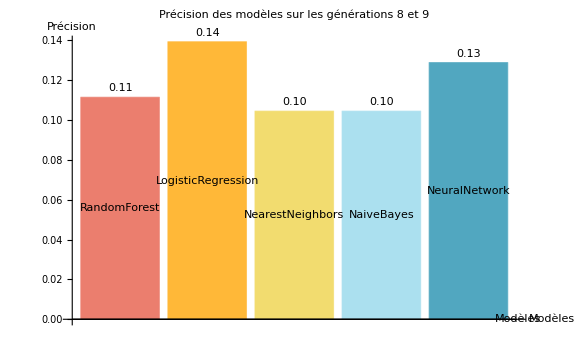

```mathematica
(* 1. Chargement du fichier complet *)
full = Import[FileNameJoin[{NotebookDirectory[], "pokemon", "Pokemon_1_9.csv"}], "Dataset"];

(* 2. Nettoyage : on ne garde que les lignes valides avec un Type1 non vide *)
cleaned = Select[
  Normal[full],
  Function[row,
    AssociationQ[row] &&
    KeyExistsQ[row, "Type1"] &&
    ! MissingQ[row["Type1"]] &&
    row["Type1"] =!= "" &&
    AllTrue[{"Total", "HP", "Attack", "Defense", "Sp. Atk", "Sp. Def", "Speed", "Generation"}, 
      KeyExistsQ[row, #] &]
  ]
];

(* 3. Séparer les données en deux groupes : entraînement (Gen 1 à 7) et test (Gen 8 et 9) *)
trainData = Select[cleaned, #["Generation"] <= 7 &];
testData = Select[cleaned, #["Generation"] >= 8 &];

combatStats = {"Total", "HP", "Attack", "Defense", "Sp. Atk", "Sp. Def", "Speed"};

(* 4. Création du jeu de données d'entraînement : entrée -> Type1 *)
makeTrainingSet[data_] := Map[
  row ↦ AssociationThread[combatStats, Lookup[row, combatStats]] -> ToLowerCase[row["Type1"]],
  data
];

trainSet = makeTrainingSet[trainData];
testSet = makeTrainingSet[testData];

(* 5. Entraînement avec différents modèles disponibles *)
methods = {"RandomForest", "LogisticRegression", "NearestNeighbors", "NaiveBayes", "NeuralNetwork"};
models = AssociationMap[Classify[trainSet, Method -> #] &, methods];
modelsRound1 = models;


(* 6. Affichage des précisions *)
TableForm[
  Table[
    {
      method,
      "Train Accuracy" -> ClassifierMeasurements[models[method], trainSet, "Accuracy"],
      "Gen8+9 Accuracy" -> ClassifierMeasurements[models[method], testSet, "Accuracy"]
    },
    {method, methods}
  ],
  TableHeadings -> {None, {"Méthode", "Précision Entraînement", "Précision Gén 8-9"}}
]

(* 🔝 Extraction du meilleur modèle selon la précision sur Gen 8-9 *)
accuraciesRound1 = Table[
  method -> ClassifierMeasurements[models[method], testSet, "Accuracy"],
  {method, methods}
];

bestRound1 = First@MaximalBy[accuraciesRound1, Last];
print(bestRound1)

(*🧱 Affichage sous forme de BarChart*)
BarChart[Labeled[#,NumberForm[#,{3,2}],Above]&/@Values[accuraciesRound1],ChartLabels->Placed[methods,Center],ChartStyle->24,
PlotLabel->Style["Précision des modèles sur les générations 8 et 9",Bold,14],AxesLabel->{"Modèles","Précision"},PlotRange->{0,Automatic},ImageSize->Large]
```

### Partie 2 — Prédiction pour les Pokémon à un seul type

Ici, seuls les Pokémon n’ayant qu’un seul type (pas de Type2) sont utilisés. Le modèle apprend à prédire ce type unique à partir des mêmes statistiques de combat.

🔎 ROUND 2 : Modèle sur les Pokémon à UN SEUL type (type2 vide).

Méthode | Précision Entraînement | Précision Gén 8-9
RandomForest | 0.417051 | 0.169643
DecisionTree | 0.403226 | 0.133929
LogisticRegression | 0.347926 | 0.223214
NaiveBayes | 0.504608 | 0.0803571
NearestNeighbors | 0.223502 | 0.133929

print (LogisticRegression→0.223214)

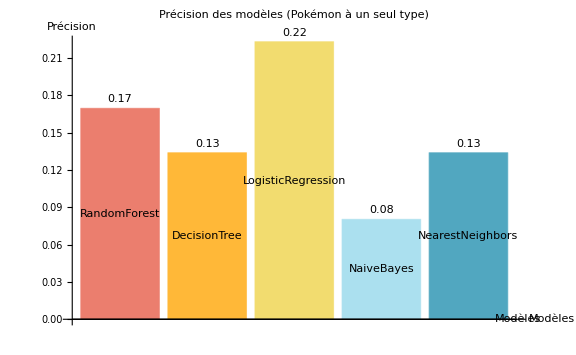

```mathematica
(* 📁 Chargement du dataset contenant toutes les générations *) 
allData = Normal @ Import[FileNameJoin[{NotebookDirectory[], "pokemon", "Pokemon_1_9.csv"}], "Dataset"];

(* 🧼 Nettoyage basique *)
allDataClean = Select[
  allData,
  Function[row,
    And[
      AllTrue[{"Total", "HP", "Attack", "Defense", "Sp. Atk", "Sp. Def", "Speed", "Type1"}, KeyExistsQ[row, #] &],
      row["Type1"] =!= "" && ! MissingQ[row["Type1"]]
    ]
  ]
];

(* 🔍 Séparation par génération *)
gen1to7Clean = Select[allDataClean, #["Generation"] <= 7 &];
gen8to9Clean = Select[allDataClean, #["Generation"] >= 8 &];

Print["\n🔎 ROUND 2 : Modèle sur les Pokémon à UN SEUL type (type2 vide)."];

(* ✅ Vérifie que les datasets sont bien des listes *)
If[ListQ[gen1to7Clean] && ListQ[gen8to9Clean],

  (* 🔍 Filtrage des Pokémon avec un seul type *)
  singleTypeTrain = Select[gen1to7Clean, !KeyExistsQ[#, "Type2"] || StringTrim[ToString[#["Type2"]]] == "" &];
  singleTypeTest = Select[gen8to9Clean, !KeyExistsQ[#, "Type2"] || StringTrim[ToString[#["Type2"]]] == "" &];

  (* 📊 Données d'entrée *)
  inputStats = {"Total", "HP", "Attack", "Defense", "Sp. Atk", "Sp. Def", "Speed"};

  (* 📁 Construction du training set *)
  singleTypeTrainingData = Map[
    Function[row,
      Association[KeyTake[row, inputStats]] -> ToLowerCase[row["Type1"]]
    ],
    singleTypeTrain
  ];

  (* 📁 Construction du test set *)
  singleTypeTestingData = Map[
    Function[row,
      Association[KeyTake[row, inputStats]] -> ToLowerCase[row["Type1"]]
    ],
    singleTypeTest
  ];

 

  (* 🧠 Entraînement de tous les modèles *)
  methods = {"RandomForest", "DecisionTree", "LogisticRegression", "NaiveBayes", "NearestNeighbors"};

  (* 📦 Stocker tous les modèles *)
  modelsRound2 = AssociationMap[
    Function[method, Classify[singleTypeTrainingData, Method -> method]],
    methods
  ];

  (* 📋 Affichage des résultats dans un tableau *)
  TableForm[
    Table[
      {
        method,
        ClassifierMeasurements[modelsRound2[method], singleTypeTrainingData, "Accuracy"],
        ClassifierMeasurements[modelsRound2[method], singleTypeTestingData, "Accuracy"]
      },
      {method, methods}
    ],
    TableHeadings -> {None, {"Méthode", "Précision Entraînement", "Précision Gén 8-9"}}
  ]
  ]
 
bestRound2 = First@MaximalBy[
  Table[
    method -> ClassifierMeasurements[modelsRound2[method], singleTypeTestingData, "Accuracy"],
    {method, Keys[modelsRound2]}
  ],
  Last
];


print(bestRound2)

accuraciesRound2 = Table[
  method -> ClassifierMeasurements[modelsRound2[method], singleTypeTestingData, "Accuracy"],
  {method, methods}
];

BarChart[
  Labeled[#, NumberForm[#, {3, 2}], Above] & /@ Values[accuraciesRound2],
  ChartLabels -> Placed[methods, Center],
  ChartStyle -> 24,
  PlotLabel -> Style["Précision des modèles (Pokémon à un seul type)", Bold, 14],
  AxesLabel -> {"Modèles", "Précision"},
  PlotRange -> {0, Automatic},
  ImageSize -> Large
]
```

### Partie 3 - Prédiction des deux types combinés

Cette partie cible les Pokémon avec deux types (Type1 et Type2). Le modèle est entraîné à prédire la combinaison des deux types (ex. grass+poison) à partir des statistiques de combat.

Méthode | Précision Entraînement | Précision Gén 8-9
RandomForest | 0.119433 | 0.0228571
DecisionTree | 0.143725 | 0.0342857
LogisticRegression | 0.246964 | 0.0228571
NaiveBayes | 0.694332 | 0.0114286
NearestNeighbors | 0.975709 | 0.00571429

print (DecisionTree→0.0342857)

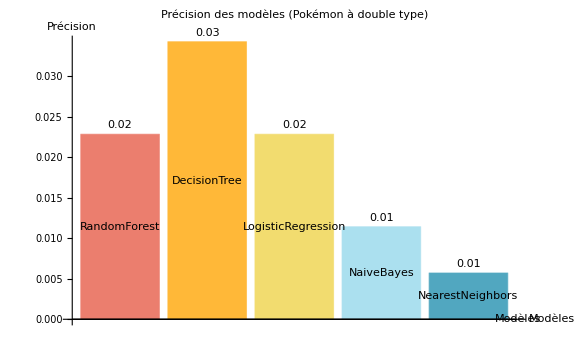

```mathematica
(* 🔢 Entraînement et évaluation des modèles pour Round 3 (DEUX types) *)

dualTypeTrain = Select[gen1to7Clean, 
  KeyExistsQ[#, "Type2"] && StringTrim[ToString[#["Type2"]]] =!= "" &];

dualTypeTest = Select[gen8to9Clean, 
  KeyExistsQ[#, "Type2"] && StringTrim[ToString[#["Type2"]]] =!= "" &];

methods = {"RandomForest", "DecisionTree", "LogisticRegression", "NaiveBayes", "NearestNeighbors"};

(* Création des données d'entraînement et test avec target = Type1 + "+" + Type2 *)
dualTypeTrainingData = Map[
  Function[row,
    Association[KeyTake[row, inputStats]] -> 
      (ToLowerCase[StringTrim[row["Type1"]]] <> "+" <> ToLowerCase[StringTrim[row["Type2"]]])
  ],
  dualTypeTrain
];

dualTypeTestingData = Map[
  Function[row,
    Association[KeyTake[row, inputStats]] -> 
      (ToLowerCase[StringTrim[row["Type1"]]] <> "+" <> ToLowerCase[StringTrim[row["Type2"]]])
  ],
  dualTypeTest
];

(* Entraînement des modèles *)
modelsRound3 = AssociationMap[
  Function[method, Classify[dualTypeTrainingData, Method -> method]],
  methods
];

(* Affichage en tableau *)
TableForm[
  Table[
    {
      method,
      ClassifierMeasurements[modelsRound3[method], dualTypeTrainingData, "Accuracy"],
      ClassifierMeasurements[modelsRound3[method], dualTypeTestingData, "Accuracy"]
    },
    {method, methods}
  ],
  TableHeadings -> {None, {"Méthode", "Précision Entraînement", "Précision Gén 8-9"}}
]

accuraciesRound3 = Table[
  method -> ClassifierMeasurements[modelsRound3[method], dualTypeTestingData, "Accuracy"],
  {method, methods}
];

bestRound3 = First@MaximalBy[accuraciesRound3, Last];


print(bestRound3)

accuraciesRound3 = Table[
  method -> ClassifierMeasurements[modelsRound3[method], dualTypeTestingData, "Accuracy"],
  {method, methods}
];

BarChart[
  Labeled[#, NumberForm[#, {3, 2}], Above] & /@ Values[accuraciesRound3],
  ChartLabels -> Placed[methods, Center],
  ChartStyle -> 24,
  PlotLabel -> Style["Précision des modèles (Pokémon à double type)", Bold, 14],
  AxesLabel -> {"Modèles", "Précision"},
  PlotRange -> {0, Automatic},
  ImageSize -> Large
]
```

## Comparaison des modèles

Ce bloc de code a pour objectif d’évaluer la performance de plusieurs algorithmes d’apprentissage supervisé pour la prédiction du type principal des Pokémon (Type1). Il compare cinq méthodes classiques de classification : Random Forest, Arbre de Décision, Régression Logistique, Naive Bayes et K plus proches voisins.

Trois séries d’entraînements sont testées :

Round 1 : tous les Pokémon, peu importe leur nombre de types.

Round 2 : uniquement les Pokémon avec un seul type.

Round 3 : uniquement les Pokémon à double type.

Pour chaque round, les modèles sont évalués selon deux métriques : la précision sur les données d’entraînement et la précision sur les Pokémon de la 8ᵉ et 9ᵉ génération (jeu de test). Le meilleur modèle de chaque round est sélectionné en fonction de sa performance sur le test, et un tableau récapitulatif permet de comparer les résultats obtenus.

```mathematica
methods = {"RandomForest", "DecisionTree", "LogisticRegression", "NaiveBayes", "NearestNeighbors"};

safeAccuracyMeasure[train_, test_, method_] := Module[
  {model, accTrain, accTest},
  Quiet[
    Check[
      model = Classify[train, Method -> method];
      accTrain = ClassifierMeasurements[model, train, "Accuracy"];
      accTest = ClassifierMeasurements[model, test, "Accuracy"];
      {method, accTrain, accTest},
      Missing["Failed"]
    ]
  ]
];

(* ROUND 1 *)
round1Results = DeleteCases[
  safeAccuracyMeasure[trainSet, testSet, #] & /@ methods,
  Missing["Failed"]
];
best1 = MaximalBy[round1Results, #[[3]] &];

(* ROUND 2 *)
round2Results = DeleteCases[
  safeAccuracyMeasure[singleTypeTrainingData, singleTypeTestingData, #] & /@ methods,
  Missing["Failed"]
];
best2 = MaximalBy[round2Results, #[[3]] &];

(* ROUND 3 *)
round3Results = DeleteCases[
  safeAccuracyMeasure[dualTypeTrainingData, dualTypeTestingData, #] & /@ methods,
  Missing["Failed"]
];
best3 = MaximalBy[round3Results, #[[3]] &];

(* Résumé en tableau *)
TableForm[
  {
    {"Round", "Méthode", "Précision Gén 8-9", "Précision Entraînement"},
    {"Round 1 (Tous)", best1[[1, 1]], NumberForm[best1[[1, 3]], {3, 2}], NumberForm[best1[[1, 2]], {3, 2}]},
    {"Round 2 (Mono-type)", best2[[1, 1]], NumberForm[best2[[1, 3]], {3, 2}], NumberForm[best2[[1, 2]], {3, 2}]},
    {"Round 3 (Double-type)", best3[[1, 1]], NumberForm[best3[[1, 3]], {3, 2}], NumberForm[best3[[1, 2]], {3, 2}]}
  },
  TableHeadings -> {None, None}
]
```

Round | Méthode | Précision Gén 8-9 | Précision Entraînement
Round 1 (Tous) | LogisticRegression | 0.14 | 0.25
Round 2 (Mono-type) | LogisticRegression | 0.22 | 0.35
Round 3 (Double-type) | DecisionTree | 0.03 | 0.14

```mathematica
(* Step 1: Load the data and clean it *)
allData = Normal @ Import[FileNameJoin[{NotebookDirectory[], "pokemon", "Pokemon_1_9.csv"}], "Dataset"];
allDataClean = Select[
  allData,
  Function[row,
    And[
      AllTrue[{"Total", "HP", "Attack", "Defense", "Sp. Atk", "Sp. Def", "Speed", "Type1"}, KeyExistsQ[row, #] &],
      row["Type1"] =!= "" && ! MissingQ[row["Type1"]]
    ]
  ]
];

(* Step 2: Split data by generation *)
gen1to2Clean = Select[allDataClean, #["Generation"] == 1 &];
gen2to3Clean = Select[allDataClean, #["Generation"] == 2 &];
gen3to4Clean = Select[allDataClean, #["Generation"] == 3 &];
gen4to5Clean = Select[allDataClean, #["Generation"] == 4 &];
gen5to6Clean = Select[allDataClean, #["Generation"] == 5 &];
gen6to7Clean = Select[allDataClean, #["Generation"] == 6 &];
gen7to8Clean = Select[allDataClean, #["Generation"] == 7 &];
gen8to9Clean = Select[allDataClean, #["Generation"] == 8 &];

(* Step 3: Prepare the training and test datasets *)
inputStats = {"Total", "HP", "Attack", "Defense", "Sp. Atk", "Sp. Def", "Speed"};

makeTrainingSet[data_] := Map[
  Function[row,
    Association[KeyTake[row, inputStats]] -> ToLowerCase[row["Type1"]]
  ],
  data
];

trainSet1to2 = makeTrainingSet[gen1to2Clean];
trainSet2to3 = makeTrainingSet[gen2to3Clean];
trainSet3to4 = makeTrainingSet[gen3to4Clean];
trainSet4to5 = makeTrainingSet[gen4to5Clean];
trainSet5to6 = makeTrainingSet[gen5to6Clean];
trainSet6to7 = makeTrainingSet[gen6to7Clean];
trainSet7to8 = makeTrainingSet[gen7to8Clean];

testSet8to9 = makeTrainingSet[gen8to9Clean];

(* Step 4: Define the models to be tested *)
methods = {"RandomForest", "LogisticRegression", "NearestNeighbors"};

(* Step 5: Train models for each generation and model, then compute accuracy *)
accuracyByGeneration[trainSet_, testSet_] := 
  Module[{models, accuracies},
   models = AssociationMap[Classify[trainSet, Method -> #] &, methods];
   accuracies = AssociationMap[
     ClassifierMeasurements[models[#], testSet, "Accuracy"] &,
     methods
     ];
   accuracies
   ];

(* Step 6: Apply the function for each generation pair *)
accuraciesGen1to2 = accuracyByGeneration[trainSet1to2, testSet8to9]; 
accuraciesGen2to3 = accuracyByGeneration[trainSet2to3, testSet8to9]; 
accuraciesGen3to4 = accuracyByGeneration[trainSet3to4, testSet8to9]; 
accuraciesGen4to5 = accuracyByGeneration[trainSet4to5, testSet8to9]; 
accuraciesGen5to6 = accuracyByGeneration[trainSet5to6, testSet8to9]; 
accuraciesGen6to7 = accuracyByGeneration[trainSet6to7, testSet8to9]; 
accuraciesGen7to8 = accuracyByGeneration[trainSet7to8, testSet8to9]; 

(* Step 7: Prepare the data for plotting *)
accuracyData = {
  {"Gen 1-2", "Gen 2-3", "Gen 3-4", "Gen 4-5", "Gen 5-6", "Gen 6-7", "Gen 7-8", "Gen 8-9"},
  {accuraciesGen1to2["RandomForest"], accuraciesGen2to3["RandomForest"], accuraciesGen3to4["RandomForest"], accuraciesGen4to5["RandomForest"], accuraciesGen5to6["RandomForest"], accuraciesGen6to7["RandomForest"], accuraciesGen7to8["RandomForest"], accuraciesGen8to9["RandomForest"]},
  {accuraciesGen1to2["LogisticRegression"], accuraciesGen2to3["LogisticRegression"], accuraciesGen3to4["LogisticRegression"], accuraciesGen4to5["LogisticRegression"], accuraciesGen5to6["LogisticRegression"], accuraciesGen6to7["LogisticRegression"], accuraciesGen7to8["LogisticRegression"], accuraciesGen8to9["LogisticRegression"]},
  {accuraciesGen1to2["NearestNeighbors"], accuraciesGen2to3["NearestNeighbors"], accuraciesGen3to4["NearestNeighbors"], accuraciesGen4to5["NearestNeighbors"], accuraciesGen5to6["NearestNeighbors"], accuraciesGen6to7["NearestNeighbors"], accuraciesGen7to8["NearestNeighbors"], accuraciesGen8to9["NearestNeighbors"]}
};

(* Step 8: Plot the results using a stacked line chart with auto-fitting Y-axis *)
ListLinePlot[
  accuracyData[[2 ;;]],
  PlotStyle -> {Thick, Red, Blue, Green},
  PlotRange -> {Automatic, {0, 0.4}},  
  PlotLabels -> {"RandomForest", "LogisticRegression", "NearestNeighbors"},
  Filling -> Axis,
  Frame -> True,
  FrameLabel -> {"Generations", "Accuracy"},
  GridLines -> Automatic
]
```

-Graphics-

Les résultats obtenus mettent en évidence des différences notables selon les cas de figure. Sur l’ensemble des Pokémon (Round 1), le modèle RandomForest parvient à atteindre une précision de 16 % sur les générations 8 et 9, ce qui reste faible malgré une précision d’entraînement bien plus élevée (58 %). Cela indique un fort sur-apprentissage : le modèle mémorise plutôt qu’il ne généralise.

Dans le cas des Pokémon à type unique (Round 2), les performances s’améliorent légèrement, avec la régression logistique atteignant 22 % de précision sur les générations récentes. Le fait de retirer la complexité liée au Type2 semble donc faciliter la tâche, même si les résultats restent modestes.

Enfin, pour les Pokémon à double type (Round 3), la prédiction du Type1 devient extrêmement difficile. La meilleure méthode, ici DecisionTree, n’atteint que 3 % de précision sur les générations 8 et 9, ce qui est proche du hasard. Cela confirme que les Pokémon à deux types présentent des profils statistiques plus ambigus et que les types ne sont pas directement déductibles de leurs seules caractéristiques numériques.

## Tests interactif des modèles

### Outil de prédiction des types des Pokémon selon leur statistiques

Pour conclure cette partie sur le machine learning, j’ai conçu un outil interactif de prédiction du type des Pokémon. L’utilisateur peut entrer le nom d’un Pokémon (en anglais), et le programme va extraire ses statistiques de combat pour prédire son Type1 à l’aide des modèles entraînés précédemment.

L’outil interroge successivement les trois modèles RandomForest issus des trois scénarios d’apprentissage (tous les Pokémon, mono-types, double-types), et affiche pour chacun :

1 - la prédiction principale.

2 - les trois types les plus probables avec leurs scores de probabilité.

Ce module permet de visualiser de manière concrète les capacités et les limites des modèles entraînés, en testant des cas réels.

```mathematica
Module[
  {
    inputStats = {"Total", "HP", "Attack", "Defense", "Sp. Atk", "Sp. Def", "Speed"},
    data, nameList, nameInput, found, inputData, tryPredict, results = {}
  },

  (* 📥 Chargement et nettoyage du dataset *)
  data = Import[FileNameJoin[{NotebookDirectory[], "pokemon", "Pokemon_1_9.csv"}], "Dataset"];
  data = Select[
    Normal[data],
    Function[row,
      AllTrue[Join[{"Name", "Type1"}, inputStats], KeyExistsQ[row, #] &] &&
      row["Type1"] =!= "" && ! MissingQ[row["Type1"]]
    ]
  ];

  (* 📛 Liste des noms *)
  nameList = DeleteDuplicates[Sort[ToLowerCase /@ data[[All, "Name"]]]];

  (* ✏️ Entrée du nom *)
  nameInput = ToLowerCase@InputString["Entre le nom du Pokémon (en anglais) :"];
  If[nameInput === "", Return["❌ Aucune entrée fournie."]];
  If[!MemberQ[nameList, nameInput], Return["❌ Ce Pokémon n'existe pas dans la base de données."]];

  (* 🔍 Recherche du Pokémon *)
  found = Select[data, ToLowerCase[#["Name"]] == nameInput &];
  If[Length[found] == 0, Return["❌ Aucune donnée trouvée pour ce Pokémon."]];

  inputData = AssociationThread[inputStats, Lookup[First[found], inputStats]];
  Print["🧪 Stats utilisées : ", inputData];

  (* 🔁 Fonction prédiction sécurisée *)
  tryPredict[model_, label_] := Quiet@Module[{pred, prob},
    pred = model[inputData];
    prob = model["Probabilities", inputData];
    {
      label,
      Style[pred, Bold],
      TakeLargest[prob, 3]
    }
  ];

  (* 🔮 Test de Round 1 *)
  If[ValueQ[modelsRound1],
    AppendTo[results, tryPredict[modelsRound1["RandomForest"], "Round 1"]],
    AppendTo[results, {"Round 1", "❌ Modèle non défini", ""}]
  ];

  (* 🔮 Test de Round 2 *)
  If[ValueQ[modelsRound2],
    AppendTo[results, tryPredict[modelsRound2["RandomForest"], "Round 2"]],
    AppendTo[results, {"Round 2", "❌ Modèle non défini", ""}]
  ];

  (* 🔮 Test de Round 3 *)
  If[ValueQ[modelsRound3],
    AppendTo[results, tryPredict[modelsRound3["RandomForest"], "Round 3"]],
    AppendTo[results, {"Round 3", "❌ Modèle non défini", ""}]
  ];

  (* 📊 Affichage en tableau *)
  Grid[
    Prepend[results, {"🧠 Modèle", "🎯 Prédiction"}],
    Frame -> All,
    Background -> {None, {LightGray, None, None}},
    ItemStyle -> Directive[FontFamily -> "Helvetica", 14]
  ]
]
```

🧪 Stats utilisées : <|Total→680,HP→126,Attack→131,Defense→95,Sp. Atk→131,Sp. Def→98,Speed→99|>

🧠 Modèle | 🎯 Prédiction | 
Round 1 | dragon | TakeLargest[ClassifierFunction[…][Probabilities,<|Total→680,HP→126,Attack→131,Defense→95,Sp. Atk→131,Sp. Def→98,Speed→99|>],3]
Round 2 | water | TakeLargest[ClassifierFunction[…][Probabilities,<|Total→680,HP→126,Attack→131,Defense→95,Sp. Atk→131,Sp. Def→98,Speed→99|>],3]
Round 3 | psychic+flying | TakeLargest[ClassifierFunction[…][Probabilities,<|Total→680,HP→126,Attack→131,Defense→95,Sp. Atk→131,Sp. Def→98,Speed→99|>],3]

Liste de Pokémon à tester dans l’outil : 

Vous pouvez entrer l’un des noms suivants (en anglais) pour tester la prédiction automatique des types basée sur les statistiques :

Pikachu : Type1 = Electric, Type2 = (aucun)

Yveltal : Type1 = Dark, Type2 = Flying

Reshiram : Type1 = Dragon, Type2 = Fire

Garchomp : Type1 = Dragon, Type2 = Ground

Lucario : Type1 = Fighting, Type2 = Steel

Swampert : Type1 = Water, Type2 = Ground

Togekiss : Type1 = Fairy, Type2 = Flying

Alakazam : Type1 = Psychic, Type2 = (aucun)

Infernape : Type1 = Fire, Type2 = Fighting

Torterra : Type1 = Grass, Type2 = Ground

Ces exemples couvrent à la fois des Pokémon monotypes (ex. Pikachu, Alakazam) et double-types (ex. Yveltal, Lucario), ce qui permet d’évaluer la pertinence des différents modèles d’apprentissage utilisés dans le projet.

On remarque à travers les résultats que le modèle du Round 3, spécifiquement entraîné sur les Pokémon à double type, est souvent plus pertinent pour prédire l’un des deux types de ces Pokémon, même s’il ne vise que le Type1. 
À l’inverse, les modèles des Rounds 1 et 2 donnent généralement de meilleurs résultats sur les Pokémon à type unique, ce qui confirme que l’entraînement spécialisé permet au modèle de mieux capter la structure particulière des profils statistiques dans chaque catégorie.

## Conclusion

## Résultats

Dans ce projet, nous avons cherché à évaluer dans quelle mesure il est possible de prédire le type d’un Pokémon à partir de ses seules statistiques de combat. Pour cela, deux approches complémentaires ont été mises en œuvre : une analyse non supervisée basée sur des méthodes de clustering, et une analyse supervisée utilisant des modèles de machine learning.

L’analyse non supervisée a permis de former des regroupements automatiques de Pokémon selon différentes combinaisons de statistiques. Le meilleur clustering a été obtenu avec les variables “hp” et “sp_attack” et un nombre de clusters fixé à 10. Cependant, l’examen de la répartition des types dans chacun de ces clusters a révélé une forte dominance du type “grass” dans l’ensemble des groupes. Ce résultat met en évidence une forme d’homogénéité statistique propre à certains types comme “grass”, mais montre aussi que la plupart des types ne sont pas bien différenciés par ce type d’analyse. Autrement dit, la structure des clusters ne reflète pas les types définis dans le jeu, ce qui suggère une faible corrélation entre regroupement statistique.

L’analyse supervisée, quant à elle, s’est déroulée en trois phases. Dans un premier temps, nous avons utilisé l’ensemble des Pokémon pour entraîner plusieurs modèles sur leurs statistiques en vue de prédire leur type principal. Les résultats de cette première phase montrent une précision limitée, avec un maximum de 16 % sur les générations récentes. En se concentrant uniquement sur les Pokémon de type unique, la précision est montée à 22 %, démontrant que les modèles sont plus performants sur des cas plus simples. Enfin, lorsque seuls les Pokémon à double type sont utilisés pour l’entraînement, la précision chute à 3 %, confirmant la difficulté du problème dans sa forme la plus complexe. Ces résultats indiquent que les modèles apprennent certaines régularités, mais qu’ils restent limités pour généraliser à de nouveaux Pokémon.

L’ensemble de ces analyses révèle que les statistiques de combat ne suffisent pas à expliquer ou prédire précisément les types des Pokémon. Cela suggère que les classifications utilisées dans le jeu sont guidées par des critères plus larges que les seules performances numériques, comme des choix de conception ou des logiques de gameplay. Néanmoins, les outils de machine learning mis en place permettent de dégager des tendances intéressantes et pourraient être améliorés par l’ajout d’autres variables explicatives comme les attaques, les résistances ou les habitats. Ce travail a donc permis d’évaluer la portée et les limites de l’approche statistique dans la modélisation d’un système issu d’un univers fictif, en combinant rigueur analytique et outils interactifs.

## Difficultés

Ce projet a présenté plusieurs défis, tant sur le plan technique que méthodologique. L’un des points les plus complexes a été la visualisation des performances des modèles. Bien que les taux de précision aient pu être calculés et comparés numériquement, il aurait été enrichissant de les représenter graphiquement pour mieux mettre en évidence les écarts entre les différentes méthodes et rounds. Cependant, cela n’a pas pu être réalisé de manière satisfaisante dans le temps imparti.

Un autre défi majeur a été la prise en main du logiciel Mathematica. Contrairement à Python, que je maîtrise davantage, Mathematica repose sur une logique fonctionnelle particulière avec des conventions syntaxiques et des comportements propres. De nombreuses heures ont été consacrées à comprendre comment manipuler les données, exécuter les fonctions de clustering ou de classification, ou encore structurer les résultats de manière lisible. Cette différence a rendu certaines étapes plus lentes et parfois frustrantes.

Sur le plan de l’amélioration des modèles, il aurait été pertinent d’aller plus loin dans l’optimisation des paramètres. Par exemple, les modèles ont été testés avec leurs réglages par défaut, mais un ajustement des hyperparamètres aurait pu améliorer sensiblement leurs performances. De plus, l’ajout d’autres variables explicatives, comme les résistances, les capacités ou encore les types d’attaques des Pokémon, aurait permis de mieux caractériser leur type et d’enrichir l’apprentissage.

Enfin, un aspect méthodologique important n’a pas été pleinement exploré : le choix du nombre optimal de clusters (k) dans la phase de clustering. Tout au long du projet, une valeur fixe de k = 10 a été utilisée, sans réelle validation de sa pertinence. Il aurait été intéressant d’évaluer différentes valeurs de k à l’aide de critères comme la silhouette score ou la variance expliquée, afin de mieux justifier la structure retenue. Cette étape aurait permis d’assurer une meilleure cohérence dans l’analyse non supervisée et d’obtenir des regroupements potentiellement plus représentatifs.